```mathematica
以下是灵敏电流计的程序,也没有编号
```

```mathematica
测量电流计常数和内电阻
```

R = 100: I = 0.0685893+0.390191 n

R = 200: I = 0.199596+0.689864 n

R = 300: I = 0.00811634+0.994173 n

R = 400: I = 0.18774+1.2948 n

R = 500: I = 0.14963+1.59237 n

R = 600: I = 0.240189+1.89017 n

R = 700: I = 0.333333+2.19 n

R = 800: I = 0.3+2.48429 n

R = 900: I = 0.364733+2.79225 n

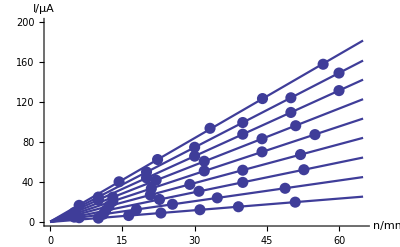

```mathematica
in[1]={10.0,3.9,16.3,6.5,23.0,9.0,31.1,
12.3,39.1,15.3,50.9,19.9};
in[2]={6.0,4.3,11.0,7.8,17.9,12.5,25.4,
17.8,34.7,24.2,48.8,33.8};
in[3]={5.0,4.9,11.5,11.5,22.7,22.6,30.9,
30.8,40.0,39.7,52.7,52.4};
in[4]={5.0,6.7,12.2,16.0,20.8,27.1,29.0,
37.7,40.0,51.9,52.0,67.6};
in[5]={5.0,8.0,13.0,20.9,21.0,33.6,32.0,
51.2,44.0,70.3,55.0,87.6};
in[6]={5.0,9.5,13.0,24.9,22.0,41.9,32.0,
60.9,44.0,83.4,51.0,96.5};
in[7]={10.0,22.1,20.0,44.3,30.0,66.0,
40.0,88.0,50.0,109.8,60.0,131.7};
in[8]={10.0,25.0,20.0,50.1,30.0,74.9,
40.0,99.7,50.0,124.5,60.0,149.3};
in[9]={6.0,16.7,14.3,40.3,22.3,62.6,
33.2,93.9,44.1,123.7,56.7,158.1};
fig={};
Do[in[i]=Partition[in[i],2];
g1=ListPlot[in[i],
PlotStyle->PointSize[0.02]];
fit=Fit[in[i],{1,n},n];
Print["R = ",i*100,":"," I = ",fit];
g2=Plot[fit,{n,0,65},
PlotStyle->Thickness[0.004]];
g=Show[{g1,g2}];AppendTo[fig,g];
in[i]=.,{i,9}]
Show[fig,PlotRange->{0,200},
AxesLabel->{"n/mm","I/μA"},
BaseStyle->{FontSize->13},
AxesStyle->Thickness[0.003]]
Clear[fit,fig,g1,g2,g]
```

```mathematica
按有效数字取舍b
```

```mathematica
t={100,0.390,200,0.689,300,0.994,400,1.29,
500,1.59,600,1.89,700,2.19,800,2.48,900,
2.79};
t=Partition[t,2];Ra=1;l=Length[t];
const={{"Kg","Rg"}};
Do[deltb=t[[j,2]]-t[[j-1,2]];
deltR=t[[j,1]]-t[[j-1,1]];kg=(Ra*deltb)/deltR;
Rg=(t[[j-1,2]]*Ra)/kg-t[[j-1,1]]-Ra;
AppendTo[const,{kg,Rg}],{j,2,l}]
SetPrecision[const,3]//TableForm
Clear[t,Ra,Rg,kg,l,const,deltb,deltR]
```

Kg | Rg
0.00299 | 29.4
0.00305 | 24.9
0.00296 | 34.8
0.003 | 29.
0.003 | 29.
0.003 | 29.
0.0029 | 54.2
0.0031 | -1.

```mathematica
观察Rg随Kg的变化
```

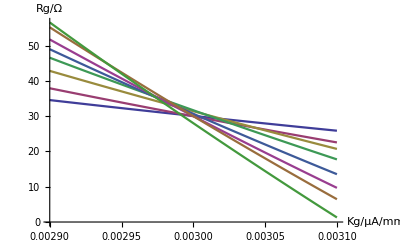

```mathematica
b={0.3902,0.6899,0.9942,1.295,1.592,1.890,
2.190,2.484};
Rg=Table[b[[i]]/Kg-i*100,{i,8}];
Plot[Evaluate[Rg],{Kg,0.0029,0.0031},
AxesLabel->{"Kg/μA/mm","Rg/Ω"},
BaseStyle->{FontSize->13},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[b,Rg]
```

```mathematica
b多保留一位
```

```mathematica
t={100,0.3902,200,0.6899,300,0.9942,400,
1.295,500,1.592,600,1.890,700,2.190,800,
2.484,900,2.792};
t=Partition[t,2];Ra=1;l=Length[t];
const={{"Kg","Rg"}};
Do[deltb=t[[j,2]]-t[[j-1,2]];
deltR=t[[j,1]]-t[[j-1,1]];kg=(Ra*deltb)/deltR;
Rg=(t[[j-1,2]]*Ra)/kg-t[[j-1,1]]-Ra;
AppendTo[const,{kg,Rg}],{j,2,l}]
SetPrecision[const,3]//TableForm
Clear[t,Ra,Rg,kg,l,const,deltb,deltR]
```

Kg | Rg
0.003 | 29.2
0.00304 | 25.7
0.00301 | 29.5
0.00297 | 35.
0.00298 | 33.2
0.003 | 29.
0.00294 | 43.9
0.00308 | 5.49

```mathematica
多取几组合
```

```mathematica
t={100,0.3902,600,1.890,200,0.6899,600,
1.890,100,0.3902,700,2.190,200,0.6899,
700,2.190,300,0.9942,700,2.190,100,0.3902,
800,2.484,200,0.6899,800,2.484,300,0.9942,
800,2.484,400,1.295,800,2.484,100,0.3902,
900,2.792,200,0.6899,900,2.792,300,0.9942,
900,2.792,400,1.295,900,2.792,500,1.592,
900,2.792};
t=Partition[t,4];len=Length[t];Ra=1;
const={{"Kg","Rg"}};
Do[δb=t[[j,4]]-t[[j,2]];δR=t[[j,3]]-t[[j,1]];
Kg=(Ra*δb)/δR;Rg=(t[[j,2]]*Ra)/Kg-t[[j,1]]-Ra;
AppendTo[const,{Kg,Rg}],{j,1,len}]
SetPrecision[const,3]//TableForm
Clear[t,Ra,Rg,Kg,len,const,δb,δR]
```

Kg | Rg
0.003 | 29.1
0.003 | 28.9
0.003 | 29.1
0.003 | 29.
0.00299 | 31.6
0.00299 | 29.5
0.00299 | 29.7
0.00298 | 32.7
0.00297 | 34.7
0.003 | 29.
0.003 | 28.7
0.003 | 30.8
0.00299 | 31.5
0.003 | 29.7

```mathematica
显示压缩过程
```

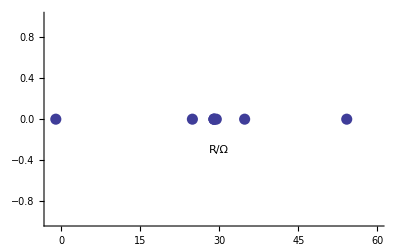

```mathematica
t={100,0.390,200,0.689,300,0.994,400,1.29,
500,1.59,600,1.89,700,2.19,800,2.48,900,
2.79};
t=Partition[t,2];Ra=1;l=Length[t];
data={};
Do[deltb=t[[j,2]]-t[[j-1,2]];
deltR=t[[j,1]]-t[[j-1,1]];kg=(Ra*deltb)/deltR;
Rg=(t[[j-1,2]]*Ra)/kg-t[[j-1,1]]-Ra;
AppendTo[data,{Rg,0}],{j,2,l}]
ListPlot[data,PlotStyle->PointSize[0.02],PlotRange->{{-2,60},{-1,1}},Axes->{True,False},AxesStyle->Thickness[0.003],Epilog->Text["R/Ω",{30,-0.3}],BaseStyle->{FontSize->13}]
Clear[t,Ra,Rg,kg,l,const,deltb,deltR]
```

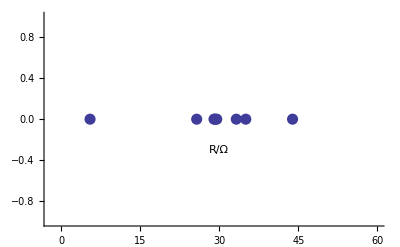

```mathematica
t={100,0.3902,200,0.6899,300,0.9942,400,
1.295,500,1.592,600,1.890,700,2.190,800,
2.484,900,2.792};
t=Partition[t,2];Ra=1;l=Length[t];
data={};
Do[deltb=t[[j,2]]-t[[j-1,2]];
deltR=t[[j,1]]-t[[j-1,1]];kg=(Ra*deltb)/deltR;
Rg=(t[[j-1,2]]*Ra)/kg-t[[j-1,1]]-Ra;
AppendTo[data,{Rg,0}],{j,2,l}]
ListPlot[data,PlotStyle->PointSize[0.02],PlotRange->{{-2,60},{-1,1}},Axes->{True,False},AxesStyle->Thickness[0.003],Epilog->Text["R/Ω",{30,-0.3}],BaseStyle->{FontSize->13}]
Clear[t,Ra,Rg,kg,l,const,deltb,deltR]
```

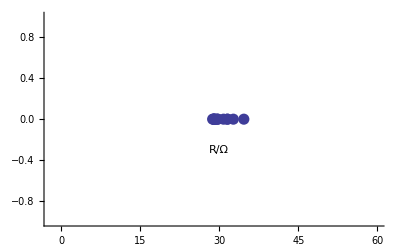

```mathematica
t={100,0.3902,600,1.890,200,0.6899,600,
1.890,100,0.3902,700,2.190,200,0.6899,
700,2.190,300,0.9942,700,2.190,100,0.3902,
800,2.484,200,0.6899,800,2.484,300,0.9942,
800,2.484,400,1.295,800,2.484,100,0.3902,
900,2.792,200,0.6899,900,2.792,300,0.9942,
900,2.792,400,1.295,900,2.792,500,1.592,
900,2.792};
t=Partition[t,4];len=Length[t];Ra=1;
data={};
Do[δb=t[[j,4]]-t[[j,2]];δR=t[[j,3]]-t[[j,1]];
Kg=(Ra*δb)/δR;Rg=(t[[j,2]]*Ra)/Kg-t[[j,1]]-Ra;
AppendTo[data,{Rg,0}],{j,1,len}]
ListPlot[data,PlotStyle->PointSize[0.02],PlotRange->{{-2,60},{-1,1}},Axes->{True,False},AxesStyle->Thickness[0.003],Epilog->Text["R/Ω",{30,-0.3}],BaseStyle->{FontSize->13}]
Clear[t,Ra,Rg,Kg,len,const,δb,δR]
```